Name : Karan Sharma
College Roll No. : 2232191
University Roll No. : 22036563079
Course : B.SC(H) Mathematics /3rd Year/ Complex Analysis
Section : A
.
PRACTICAL : 6                                                                                                                   

Q-). Show that image of half plane {z : Re[z]>1/2} under the linear transformation ω = f(z) = 1/2 is the disk { ω : |ω-1| < 1}.

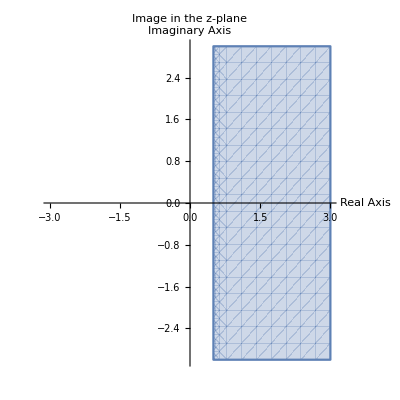

```mathematica
a= RegionPlot[Re[z]>=1/2,{x,-3,3},{y,-3,3}, Axes->True,Frame->False,AxesOrigin->{0,0,0},AxesLabel->{"Real Axis","Imaginary Axis"},PlotLabel->"Image in the z-plane"]
```

```mathematica
f[z_]:=1/z
```

```mathematica
ω=ComplexExpand[f[z]]
```

x/(x^2+y^2)-(ⅈ y)/(x^2+y^2)

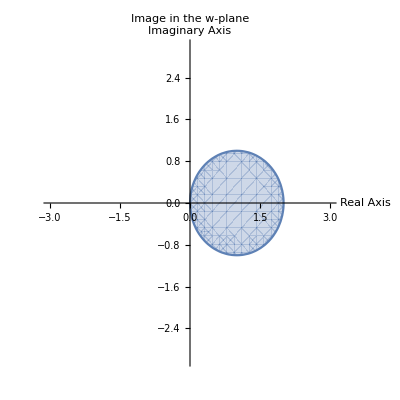

```mathematica
b= RegionPlot[Re[1/z]>=1/2,{x,-3,3},{y,-3,3}, Axes->True,Frame->False,AxesOrigin->{0,0,0},AxesLabel->{"Real Axis","Imaginary Axis"},PlotLabel->"Image in the w-plane"]
```

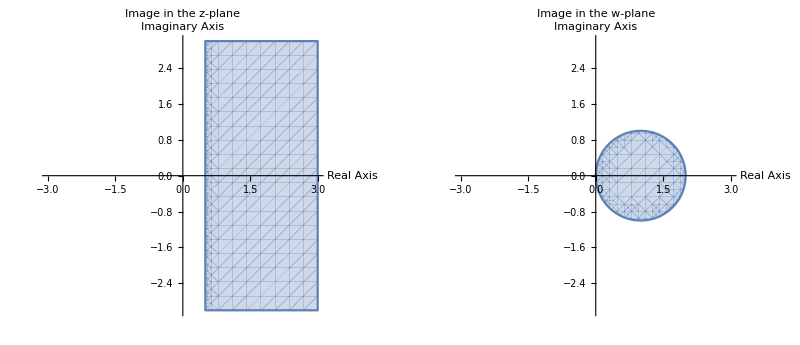

```mathematica
GraphicsRow[{a,b},Frame->All]
```